```mathematica
<<GraphUtilities`
<<Combinatorica`
Needs["MATLink`"]
OpenMATLAB[]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

MinimumVertexColoring::shdw: Symbol "MinimumVertexColoring" appears in multiple contexts {"Combinatorica`", "Notebook$$15$443087`"}; definitions in context "Combinatorica`" may shadow or be shadowed by other definitions. ButtonBox["»", Appearance->{Automatic, None}, BaseStyle->"Link", ButtonData:>"paclet:ref/message/General/shdw", ButtonNote->"Combinatorica`MinimumVertexColoring::shdw"]

MGet::shdw: Symbol "MGet" appears in multiple contexts {"MATLink`", "Notebook$$15$443087`"}; definitions in context "MATLink`" may shadow or be shadowed by other definitions.

MEvaluate::shdw: Symbol "MEvaluate" appears in multiple contexts {"MATLink`", "Notebook$$15$443087`"}; definitions in context "MATLink`" may shadow or be shadowed by other definitions.

OpenMATLAB::wspo: The MATLAB workspace is already open.

```mathematica
Do[MEvaluate[StringJoin["load('C:\\Users\\Kha\\OneDrive\\Lam viec\\Great Circles Problem\\MATLAB Code\\Data\\19-Feb-2015 - 8 Great Circles - 1000\\",IntegerString[i],"\\Data.mat'); close all"]];AdjacencyMat = IntegerPart[MGet["AdjacencyMatrix"]];g[i]=AdjacencyGraph[AdjacencyMat,GraphLayout->"TutteEmbedding", VertexLabels->Placed["Name",Above ],VertexLabelStyle->Directive[Black,8],VertexSize->Large];, {i,{56,57,59,60,62,64,65,66,68,70,71,72,73,76,77,81,83}}];
Do[mvc=MinimumVertexColoring@ToCombinatoricaGraph[g[i]]; 
GColored[i]=SetProperty[g[i],System`VertexStyle->Thread[System`VertexList[g[i]]->(ColorData[97]/@mvc)]]; 
Export[StringJoin["Graph ", IntegerString[i], ".pdf"],
GColored[i]], {i,{56,57,59,60,62,64,65,66,68,70,71,72,73,76,77,81,83}}];
```

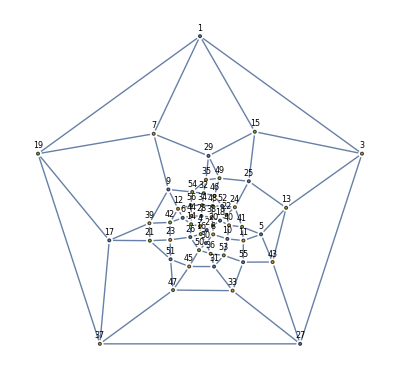

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
GColored[43]
GColored[46]
GColored[47]
GColored[48]
GColored[49]
GColored[51]
GColored[53]
GColored[54]
```

```mathematica
"
```